## QCD Parameters

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

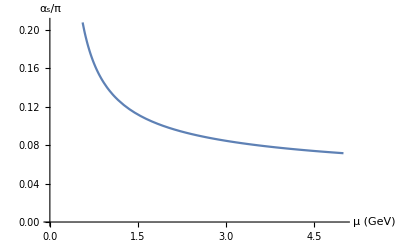

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

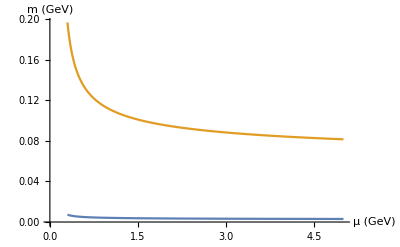

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules

### QCD Parameters

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=3,b0},
b0=(1/(12π))(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Clear[mq,ms]
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

```mathematica
αGG=0.075
```

0.075

```mathematica
M0=√0.8
```

0.894427

```mathematica
gggGGG=8.2 αGG
```

0.615

### Sum-Rules and Moments

```mathematica
Clear[gaussian]
```

```mathematica
gaussian[
k_/;k≥0&&NumericQ[k],
sHat_?NumericQ,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=terms[[1]] Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=terms[[2]]Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]] Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=terms[[4]] Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=terms[[5]]Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*terms[[7]] Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

(1/(√(4π τ)))NIntegrate[t^k Exp[(-(sHat-t)^2)/(4τ)](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[moment]
```

```mathematica
moment[
k_Integer/;k≥0,
0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

NIntegrate[t^k(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
1,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

NIntegrate[t^(k+1)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
2,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

NIntegrate[t^k(t^2+2τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
3,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

NIntegrate[t^(k+1)(t^2+6τ)(-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
moment[
k_Integer/;k≥0,
n_Integer/;n≥4,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
a=Switch[channel,"0++",(-1)/(480 π^3),"1-+",(-1)/(240 π^3),"0--",(-1)/(480 π^3),"1+-",(-1)/(240 π^3),"0-+",(-1)/(480 π^3),"1++",(-1)/(240 π^3),"0+-",(-1)/(480 π^3),"1--",(-1)/(240 π^3)];
b=Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)];d=Switch[channel,"0++",1/(24π),"1-+",(-1)/(36π),"0--",1/(24π),"1+-",(-1)/(36π),"0-+",(-1)/(24π),"1++",1/(36π),"0+-",(-1)/(24π),"1--",1/(36π)];
e=Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",(-19)/(72π),"0-+",-1/(9π),"1++",0,"0+-",(-11)/(72π),"1--",19/(72π)];
f=0*Switch[channel,"0++",(-1)/(192 π^2),"1-+",1/(192 π^2),"0--",(-1)/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",(-5)/(192 π^2),"0+-",5/(192 π^2),"1--",(-5)/(192 π^2)];

NIntegrate[t^k(1/(√(4π τ)))Integrate[sHat^n Exp[(-(sHat-t)^2)/(4τ)],{sHat,-∞,∞}](-d t αGG-αs(a t^3+b m^2 t^2+c t mψψ+e mgψσGψ-4/π f gggGGG)),{t,0,s0}]
]
```

```mathematica
Clear[normalGauss,σSquared,Athree]
```

```mathematica
normalGauss[
k_Integer/;k≥0,
sHat_?NumericQ,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=gauss[k,sHat,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]
```

```mathematica
σSquared[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^2
```

```mathematica
Athree[
k_Integer/;k≥0,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&)
]:=moment[k,3,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type]-3(moment[k,2,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])+2(moment[k,1,τ,s0,channel,type]/moment[k,0,τ,s0,channel,type])^3
```

## Holder Inequalities

```mathematica
holder[s_,alpha_,beta_,τ_,τ1_,τ2_,s0_,jpc_?StringQ,flavor_?StringQ,terms_:Table[1,{7}]]:=If[(gaussian[alpha/ω,s,τ1,s0,jpc,flavor,terms]===ComplexInfinity),2,If[((gaussian[alpha/ω,s,τ1,s0,jpc,flavor,terms]>0)&&(Im[gaussian[alpha/ω,s,τ1,s0,jpc,flavor,terms]]==0)),
Max[Table[gaussian[alpha+beta,s,τ,s0,jpc,flavor,terms]/((τ1/τ)^(ω/2)(τ2/τ)^((1-ω)/2)gaussian[alpha/ω,s,τ1,s0,jpc,flavor,terms]^ω gaussian[beta/(1-ω),s,τ2,s0,jpc,flavor,terms]^(1-ω)),{ω,0.1,0.9,0.1}]//Chop],2]
]
(*ADD IF STATEMENT on Subscript[G, k](Subscript[τ, 1],s)*)
```

```mathematica
(*Clear[s,s0,τ,δτ,ω]
s=42.;
s0=25.;
τ=2;
δτ=0.1;
holder[s,0,0,(τ(τ+δτ))/((τ+δτ) ω+τ(1-ω)),τ,τ+δτ,s0,"0+-","light"]*)
```

## Procedure

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"1--"(*, "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"*)};
flavorTable={"strange"(*,"strange"*)};
(*alpha=0;
beta=0;
s0=25;
jpc="0+-";
flavor="light";
τ1=τ;
τ2=τ+δτ;
δτ=0.1;*)
(*END PARAMETERS*)

(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor,s0,alpha,beta,τ1,τ2,δτ,ω];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
alpha=0;
beta=0;
s0=9.7;
τ1=τ;
τ2=τ+δτ;
δτ=0.1;

holderTable[jpc,flavor]=Table[{τ,s,holder[s,alpha,beta,(τ1 τ2)/(τ2 ω+τ1(1-ω)),τ1,τ2,s0,jpc,flavor]},{τ,0,100,1},{s,-100,100,1}];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-holderInequality",ToString[flavor],"_",
ToString[jpc]];
input=holderTable[jpc,flavor];
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
]
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,9.7}}.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,9.7}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,9.7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.21235}. NIntegrate obtained 6.×10^-323 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 3.84993×10^-162 9.72665×10^-148 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.00698×10^-194 2.4568×10^-118 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.04625×10^-226 6.20552×10^-89 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Max::nord: Invalid comparison with -0.0407367-0.125375 ⅈ attempted.

Max::nord: Invalid comparison with 0.-0.333881 ⅈ attempted.

Max::nord: Invalid comparison with 0.0583523+0.080315 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.